```mathematica
Get["sac.m",Path->NotebookDirectory[]];
```

```mathematica
?sac`*
```

```mathematica
history=Simulate[300,30000];
```

```mathematica
effectiveHistory=Take[history,-20000];
```

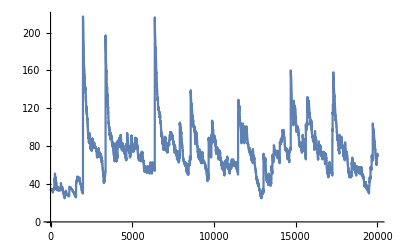

```mathematica
ListPlot[Unemployed[effectiveHistory],Joined->True,PlotRange->All]
```

```mathematica
firmHistories=FirmHistories[effectiveHistory];
```

```mathematica
firmProfitRates=FirmProfitRates[firmHistories];
```

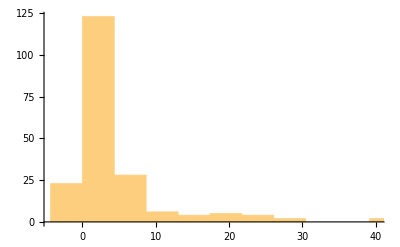
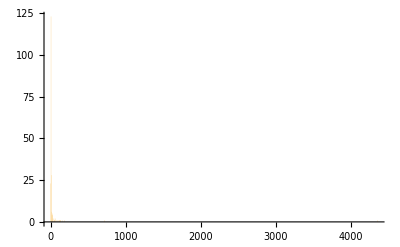

```mathematica
{Histogram[firmProfitRates],Histogram[firmProfitRates,PlotRange->All]}
```

```mathematica
firmSizes=FirmSizes[effectiveHistory];
```

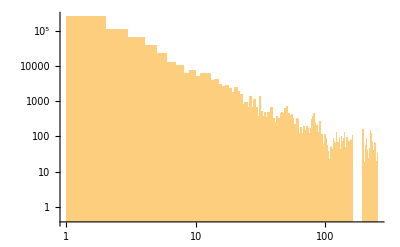

```mathematica
(* Should be a straight line *)
Histogram[firmSizes,PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

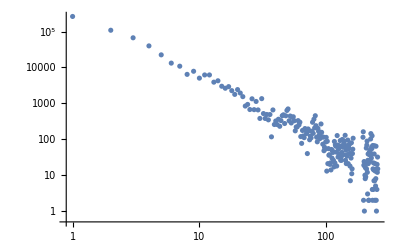

```mathematica
(* Should be a straight line *)
ListPlot[Drop[BinCounts[firmSizes],1],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
EstimatedDistribution[firmSizes,ZipfDistribution[a,b]]
```

ZipfDistribution[255,0.680898]

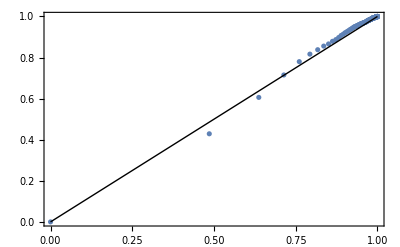

```mathematica
ProbabilityPlot[firmSizes,ZipfDistribution[a,b],PlotRange->All]
```

```mathematica
workersMoney=EmployeesMoney[effectiveHistory];
```

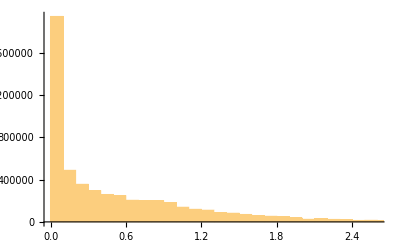

```mathematica
Histogram[workersMoney]
```

```mathematica
workersMoneySample=RandomSample[workersMoney,Round[Length[workersMoney]*0.01]];
```

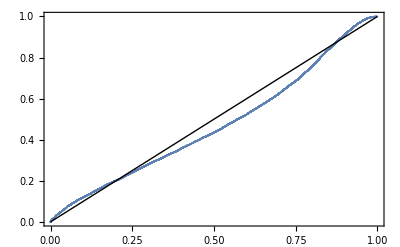

```mathematica
ProbabilityPlot[workersMoneySample,GammaDistribution[a,b]]
```

```mathematica
FindDistribution[workersMoneySample,TargetFunctions->"Continuous",MaxItems->3,PerformanceGoal->"Quality"]
```

ParetoDistribution[7.,6.39877,1.73067,-1.0011×10^-12]

```mathematica
employersWealth=EmployersWealth[effectiveHistory];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersWealth,ParetoDistribution[a,b,d]]
```

ParetoDistribution[128.905,34.7298,0.000762826]

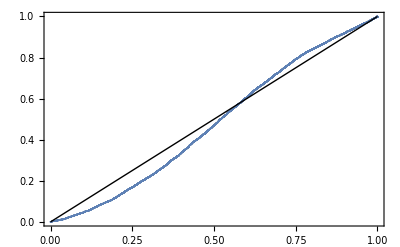

```mathematica
ProbabilityPlot[employersWealth,ParetoDistribution[a,b,d]]
```